This file contains a simple example on using NVSim in conjunction with NVHamiltonian.

```mathematica
Quit[]
```

## Needs

Of course you need the package NVSim (which needs NVHamiltonian and QuantumUtils)

```mathematica
Needs["NVSim`"]
```

Using QuantumUtils version 247.

```mathematica
FillConstants[$physicalConstants];
FillConstants[$units];
```

## Hamiltonian

### the actual hamiltonian and controls

I will perform the calculations in the interaction frame ω_rf S_z^2 with ω_rf=Δ

Here are some typical values... I’m choosing a zeeman frequency of 100MHz and Rabi of 10MHz

```mathematica
ωe=100 10^6; ω1=10 10^6;
```

The internal Hamiltonian in the interaction frame is

```mathematica
Hint=NVHamiltonian[{"B"->{(2π ωe)/γe × 10^4,0,0},"zfsActivated"->False}];
```

And the control Hamiltonians in the interaction frame

```mathematica
Hcs={2π ω1 Sx,2 π ω1 Syp};
```

## Rabi flopping using Phase Ramping

Presumably, you will have a particular pulse you want to simulate, but below I show how to create a pulse.

### simulate

This function makes a phase ramping pulse: Cos on Sx and Sin on Sy. The pulse file has the format [dt amp1 amp2 .... ] where the amps correspond to the control hamiltonians. The amps are fractions of 1, which will be multiplied by an overall power. This is to match with the experimental implementation.

```mathematica
MakePhaseRampPulse[ω_,T_,dt_]:=Table[{dt,Cos[ 2π ω t],Sin[ 2π ω t]},{t,dt/2,T-dt/2,dt}]
```

The pulsefile is just a txt file that

```mathematica
pulsefile=Export["ramppulse.dat",MakePhaseRampPulse[ωe,400 10^-9,1 10^-9]//N];
```

and the Unitaries after each time step can be calculated as follows

```mathematica
Us=EvalPulse[Hint,{pulsefile,Hcs},SimTrace->True];
```

### Plotting

Say I want to plot  the population of the ground state given that the intial state is the ground state

```mathematica
g={{0},{1},{0}};
```

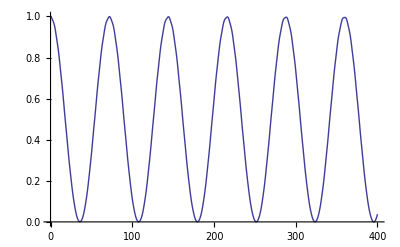

```mathematica
ListLinePlot[Abs[Tr[(g.g†).#.(g.g†).#†]]&/@Us,PlotRange->{0,1},DataRange->{0,400}]
```